```mathematica
datalambda={366,405,436,578,546,405}; (*nm*)
```

```mathematica
dataV0={1.472,1.181,1.035,0.417,0.521}; (*V*)
```

```mathematica
data={{819.1050765,1.472},{740.2282914,1.181},{687.5973807,1.035},{518.6720727,0.417},{549.0704359,0.521}}; (*THz,V*)
```

```mathematica
fit=NonlinearModelFit[data,A*x-B,{A,B},x]
```

FittedModel[…]

```mathematica
fit[{"BestFit","ParameterTable"}]
```

{-1.40113+0.00350914 x, | Estimate | Standard Error | t-Statistic | P-Value
A | 0.00350914 | 0.0000644093 | 54.4819 | 0.0000136203
B | 1.40113 | 0.0433237 | 32.341 | 0.0000649704}

```mathematica
plotfit=Plot[fit[x],{x,400,1000},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},PlotStyle->{Blend[{Blue,White}],Thick},PlotRange->{{500,850},{0.35,1.55}},Frame->True,FrameLabel->{Style["ν / THz",Bold,16],Style["V₀ / eV",16,Bold]}];
```

```mathematica
plotdata=ListPlot[data,PlotStyle->{Black,Thickness[0.003]}];
```

```mathematica
(*errores*)
```

```mathematica
errnu[A_]:=((3*10^8/((datalambda[[A]]*10^(-9))^2))*10^(-9))/(10^12);
```

```mathematica
Needs["ErrorBarPlots`"]
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
errV0[B_]:=(0.8/100)*dataV0[B]+5*10^(-3);
```

```mathematica
dataerr=ErrorListPlot[{{{819.1050765,1.472},ErrorBar[errnu[1],errV0[1]]},{{740.2282914,1.181},ErrorBar[errnu[2],errV0[2]]},{{687.5973807,1.035},ErrorBar[errnu[3],errV0[3]]},{{518.6720727,0.417},ErrorBar[errnu[4],errV0[4]]},{{549.0704359,0.521},ErrorBar[errnu[5],errV0[5]]}},AxesOrigin->{0,0},PlotStyle->{Black,Thickness[0.003]}];
```

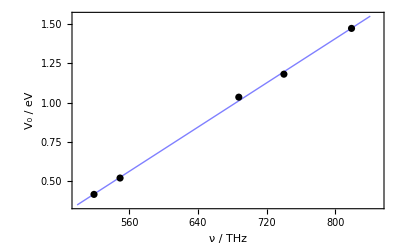

```mathematica
Show[plotfit,dataerr]
```

```mathematica
h=0.0035091437335052103*(1.6*10^(-19))*(10^(-12))
```

5.61463×10^-34

```mathematica
errh=0.00006440930189944201*(1.6*10^(-19))*(10^(-12))
```

1.03055×10^-35

```mathematica
hpdg=2*Pi*(1.054571817*10^(-34))
```

6.62607×10^-34

```mathematica
errabs=Norm[h-hpdg]
```

1.01144×10^-34

```mathematica
errrel=errabs/hpdg
```

0.152646

```mathematica
(*-----------------------------------------------------------------*)
```

```mathematica
(*CON EL APARATO DE LA CTE DE PLANCK*)
```

```mathematica
datalambda2={525,505,588,611,472}*10^(-9); (*en m*)
```

```mathematica
datanu2=N[299792458/datalambda2]*10^(-12); (*en THz*)
```

```mathematica
dataW2={0.419,0.475,0.149,0.081,0.650};(*en eV*)
```

```mathematica
data2=Transpose[{datanu2,dataW2}];
```

```mathematica
fit2=NonlinearModelFit[data2,A*x-B,{A,B},x]
```

FittedModel[…]

```mathematica
fit2[{"BestFit","ParameterTable"}]
```

{-1.85965+0.00395389 x, | Estimate | Standard Error | t-Statistic | P-Value
A | 0.00395389 | 0.000123258 | 32.0781 | 0.0000665772
B | 1.85965 | 0.0693453 | 26.8172 | 0.000113778}

```mathematica
plotfit2=Plot[fit2[x],{x,400,1000},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},PlotStyle->{Blend[{Blue,White}],Thick},PlotRange->{{460,650},{0,0.68}},Frame->True,FrameLabel->{Style["ν / THz",Bold,16],Style["V₀ / eV",16,Bold]}];
```

```mathematica
(*errores*)
```

```mathematica
errnu2[A_]:=((3*10^8/((datalambda2[[A]])^2))*10^(-9))/(10^12);
```

```mathematica
errV02[B_]:=(0.5/100)*dataW2[[B]]+3*10^(-3);
```

```mathematica
dataerr2=ErrorListPlot[{{{datanu2[[1]],dataW2[[1]]},ErrorBar[errnu2[1],errV02[1]]},{{datanu2[[2]],dataW2[[2]]},ErrorBar[errnu[2],errV0[2]]},{{datanu2[[3]],dataW2[[3]]},ErrorBar[errnu2[3],errV02[3]]},{{datanu2[[4]],dataW2[[4]]},ErrorBar[errnu2[4],errV02[4]]},{{datanu2[[5]],dataW2[[5]]},ErrorBar[errnu2[5],errV02[5]]}},AxesOrigin->{0,0},PlotStyle->{Black,Thickness[0.003]}];
```

```mathematica
plotdata2=ListPlot[data2,PlotStyle->{Black,Thickness[0.003]}];
```

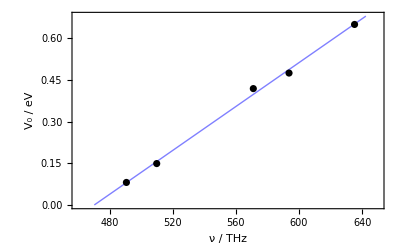

```mathematica
Show[plotfit2,dataerr2]
```

```mathematica
h2=0.003953889097949258*(1.6*10^(-19))*(10^(-12))
```

6.32622×10^-34

```mathematica
errh2=0.00012325801595869084*(1.6*10^(-19))*(10^(-12))
```

1.97213×10^-35

```mathematica
errrel2=Norm[h2-hpdg]/hpdg
```

0.0452527